# Quadratic Cost Sharing Model

A consumer that consumes x of the sharing good has utility :

```mathematica
u[x_]:=2*α*x-x^2;
```

The parameter α determines how much the consumer values consuming the good. In the absence of rental costs, α is the amount consumed by that user, conditional upon purchasing. Note that a Cobb-Douglas style utility function does not “work” as everyone consumes at least a little of the good. 
We also need a money-metric utility function so that we can accomodate rental income and rental expenses.

```mathematica
sol=Solve[u'[x]==0,x]
xstar = x/.sol[[1]];
```

{{x→α}}

```mathematica
sol2 = Solve[xstar==1,α]
```

{{α→1}}

Indirect utility :

```mathematica
v[α_]=u[xstar]
```

α^2

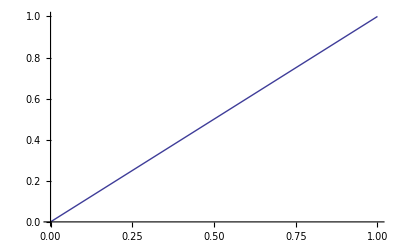

```mathematica
Plot[xstar,{α,0,1},AxesOrigin->{0,0}]
```

## Consumer purchase decision

A consumer must decide whether to purchase the good at a price p or go without.   
Everyone with an α greater than the square root of the price purchases the good.

```mathematica
Solve[p == v[α],α]
```

{{α→-√p},{α→√p}}

### Four Consumer possibilities :

1) Everyone buys: αL >  √p     (think tootbrush)

2) High types buy but low types do not: αH >  √p > αL   (think vacation homes)

3) No one buys: αH < √p  (mainframe computers in the 1950s)

## When P2P renting is possible

Let us define the short-run as the period of time before anyone can revise their purchase decisions. The consumer’s new optimization problem is:

```mathematica
uR[x_]:=2*α*x-x^2-r*x; 
solR=Collect[Solve[uR'[x]==0,x],α]
```

{{x→-r/2+α}}

Note that for the renter to consume any of the good, 2 α > r.

Optimal usage in the presence of renting (for owners) :

```mathematica
uO[x_]:=2*α*x-x^2+ (1-x)*r; 
solO=Collect[Solve[uO'[x]==0,x],α]
```

{{x→-r/2+α}}

```mathematica
xstar2[r_,α_]=x/.solR[[1]]
```

-r/2+α

### Existence and Uniqueness of a P2P Rental Equilibrium

So long as there is not a glut (i.e., the comined consumption of the two types is greater than 1) a market clearing P2P rental equilibrium exists.

```mathematica
Solve[1-xstar2[r,αH]==xstar2[r,αL],r]
```

{{r→-1+αH+αL}}

### Indirect Utility for Both Types (assuming no product market changes)

For renters :

```mathematica
vR[α_,r_]=uR[xstar2[r,α]]//FullSimplify
```

1/4 (r-2 α)^2

Comparative Statics

```mathematica
vR[α,r]/.{α->αL, r->-1+αH + αL}
```

1/4 (-1+αH-αL)^2

```mathematica
1/4 (-1*((1-αH)+αL))^2
```

```mathematica
1/4 (-1+αH-αL)^2==1/4 ((1-αH)+αL)^2//FullSimplify
```

True

A renter's surplus is increasing in their valuation parameter α.

```mathematica
Resolve[ForAll[{α,r},2α>r,D[vR[α,r],α]>0]]
```

True

A renter's surplus is decreasing in the rental rate, r.

```mathematica
D[vR[α,r],r]
```

1/2 (r-2 α)

```mathematica
vR[α,r]
```

1/4 (r-2 α)^2

```mathematica
Resolve[ForAll[{α,r}, 2*α>r, D[vR[α,r],r]<0]]
```

True

### Change in indirect utility for owners

```mathematica
uO[x]
```

r (1-x)-x^2+2 x α

```mathematica
xstar2[r,α]
```

-r/2+α

```mathematica
vO[α_,r_] = uO[xstar2[r,α]]-αH^2/.{α->αH,r->-1 +αH + αL}//FullSimplify
```

```mathematica
D[-1/4 (-3+3 αH-αL) (-1+αH+αL),αH]//FullSimplify
```

```mathematica
Reduce[1/2 (3(1- αH)-αL)<0&&αH > αL && (1-αH) < αL&&αL>0 && αH < 1]
```

(0<αL≤3/4&&(3-αL)/3<αH<1)||(3/4<αL<1&&αL<αH<1)

```mathematica
D[-1/4 (-3+3 αH-αL) (-1+αH+αL),αL]//FullSimplify
```

1/2 (1-αH+αL)

```mathematica
1/4 r (4+r-4 αH)/.{r->-1 + αH + αL}
```

```mathematica
1/4 (3(1- αH)+αL) (-1+αH+αL)
```

```mathematica
Expand[1/4 (3-3 αH+αL) (-1+αH+αL)]
```

-3/4+(3 αH)/2-(3 αH^2)/4+αL/2-(αH αL)/2+αL^2/4

```mathematica
1/4 (3(1- αH)+αL) (-1+αH+αL)
```

```mathematica
Collect[1/4 r (4+r-4 αH)/.{r->-1 + αH + αL},{αH,αL}]
```

```mathematica
□_□-3/4-(3 αH^2)/4+αH (3/2-αL/2)+αL/2+αL^2/4
```

```mathematica
r+r^2/4-r αH+αH^2/.{r->-1 + αH + αL}//FullSimplify
```

1/4 (-3+αH (6+αH)+2 αL-2 αH αL+αL^2)

```mathematica
vO[α_,r_] = uO[xstar2[r,α]]-αH^2/.{α->αH,r->-1 +αH + αL}//FullSimplify
```

```mathematica
uO[xstar2[Subscript[p, 0],αH]]
```

2 α (αH-p_0/2)-(αH-p_0/2)^2+r (1-αH+p_0/2)

```mathematica
δU = uO[xstar2[Subscript[p, 0],αH]]-(Subscript[p, 0]+δp) - (αH^2 - Subscript[p, 0])/.{r->(Subscript[p, 0]+δp),α->Subscript[p, 0]}//FullSimplify
```

```mathematica
Solve[-αH (2 αH+δp)+1/4 (4+8 αH+2 δp-3 Subscript[p, 0]) Subscript[p, 0]==0,δp]//FullSimplify
```

{{δp→-2-αH+(3 p_0)/2+(2 (-2+αH) αH)/(-2 αH+p_0)}}

```mathematica
D[-αH (2 αH+δp)+1/4 (4+8 αH+2 δp-3 Subscript[p, 0]) Subscript[p, 0],δp]
```

-αH+p_0/2

```mathematica
D[δU,δp]
```

-α+1/2 (δp+p_0)

An increase in product - market price is bad for utility so long as :

```mathematica
Reduce[D[δU,δp]<0&&α^2>Subscript[p, 0]&&α^2>(Subscript[p, 0]+δp)&&α>0&&α<1&&Subscript[p, 0]>0 && δp > 0]
```

0<α<1&&0<p_0<α^2&&0<δp<α^2-p_0

```mathematica
(2 α-Subscript[p, 0])-2 √(α^2-Subscript[p, 0])
```

2 α-2 √(α^2-p_0)-p_0

```mathematica
(2 α-2 √(α^2-Subscript[p, 0])-Subscript[p, 0])/Subscript[p, 0]//FullSimplify
```

-(-2 α+2 √(α^2-p_0)+p_0)/p_0

```mathematica
Collect[Subscript[p, 0]+1/4 Subscript[p, 1] (-4 α+Subscript[p, 1]),Subscript[p, 1]]
```

p_0-α p_1+p_1^2/4

```mathematica
Solve[Subscript[p, 0]-α Subscript[p, 1]+Subscript[p, 1]^2/4==0,Subscript[p, 1]]
```

{{p_1→2 (α-√(α^2-p_0))},{p_1→2 (α+√(α^2-p_0))}}

```mathematica
Collect[r+r^2/4-r α+α^2,r]
```

r^2/4+r (1-α)+α^2

A owner' s surplus is increasing in their valuation parameter.

```mathematica
D[vR[α,r],α]
```

-r+2 α

A owner' s surplus is increasing in the rental rate.

```mathematica
D[vO[α,r],r]
```

1+r/2-α

```mathematica
Resolve[ForAll[{α,r}, α>0 &&α < 1 && 2*α>r &&r>0, D[vO[α,r],r]>0]]
```

True

### Change in Utility Verus the Status Quo (with no product market changes)

```mathematica
conditions := α>0 &&α < 1 && 2*α>r &&r>0
```

```mathematica
vO[α,r]-v[α]//FullSimplify
```

1/4 r (4+r-4 α)

Owner utility increases with the possibility of P2P rental

```mathematica
Resolve[ForAll[{α,r}, conditions,vO[α,r]-v[α]>0]]
```

True

A renter’s utility increases with the possibility of P2P rental

```mathematica
Resolve[ForAll[{α,r}, conditions,vR[α,r]>0]]
```

True

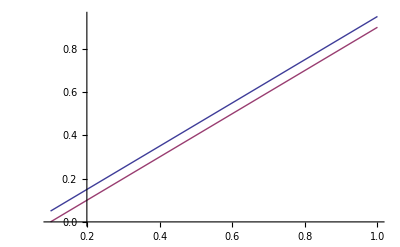

```mathematica
Plot[{xstar2[0.1,α],xstar2[0.2,α]},{α,.1,1}]
```

```mathematica
Solve[(1-xstar[r,αH])==xstar[r,αL],r]//FullSimplify
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[α[r,αH]+α[r,αL]==1,r]

```mathematica
?Dashed
```

Dashed is a graphics directive specifying that lines that follow should be drawn dashed.

```mathematica
Manipulate[Plot[α - r/2/.(r->-1+αH + αL),
 {α,0,1},PlotStyle->{Thick,Black},
PlotRange->{-0.10,1.1},
AxesLabel->{"α", "x"},
Ticks->None,
Epilog->
{
{Thick, Line[{{αL,0},{αL,αL-r/2}/.(r->-1+αH + αL)}]},
{Thick, Line[{{αH,1},{αH,αH-r/2}/.(r->-1+αH + αL)}]},
{Dashed, Line[{{αH,0},{αH,αH-r/2}/.(r->-1+αH + αL)}]},
Line[{{0,0},{1,1}}], 
Text["α_H",{αH,-0.05}],
Text["α_L",{αL,-0.05}],
Text["x^*(0)", {.92,1}],
Text["x^*(r^*)", {.92,1-r/2}/.(r->-1+αH + αL)],
}],{{αL,0.25},0,1},{{αH,0.75},0,1}]
```

```mathematica
g=DynamicModule[{αH=0.75,αL=0.5650000000000001},Plot[α-r/2/.r->-1+αH+αL,{α,0,1},PlotStyle->{Thick,Black},PlotRange->{-0.1,1.1},AxesLabel->{"α","x"},Ticks->None,Epilog->{{Thick,Line[{{αL,0},{αL,αL-r/2}/.r->-1+αH+αL}]},{Thick,Line[{{αH,1},{αH,αH-r/2}/.r->-1+αH+αL}]},{Dashed,Line[{{αH,0},{αH,αH-r/2}/.r->-1+αH+αL}]},Line[{{0,0},{1,1}}],Text["\!\(\*SubscriptBox[\(α\), \(H\)]\)",{αH,-0.05}],Text["\!\(\*SubscriptBox[\(α\), \(L\)]\)",{αL,-0.05}],Text["\!\(\*SuperscriptBox[\(x\), \(*\)]\)(0)",{0.92,1}],Text["\!\(\*SuperscriptBox[\(x\), \(*\)]\)(\!\(\*SuperscriptBox[\(r\), \(*\)]\))",{0.92,1-r/2}/.r->-1+αH+αL],Null}]];
```

```mathematica
Export["../writeup/diagrams/market_clearing.pdf",g]
```

../writeup/diagrams/market_clearing.pdf

### Equilibrium Rental Rate

{{r→-1+αH+αL}}

Comment : If either the high or low types value the good more, the rental rate increases. An increase in αH reduces supply, whereas an increase in αL reduces demand.

```mathematica
Solve[-1+αH+αL==αH^2,αH]//FullSimplify
```

{{αH→1/2 (1-√(-3+4 αL))},{αH→1/2 (1+√(-3+4 αL))}}

```mathematica
g1 = RegionPlot[αH^2 > p &&αH > αL/.p->0.5,{αL, 0,1}, {αH,0,1},PlotLegends->"Expressions",MeshFunctions->{#1+#2&},Mesh->{Range[-2 Pi,2 Pi,Pi/50]},PlotStyle->None]; 
g2 = RegionPlot[αL^2 < p && αH > αL /.p->0.5,{αL, 0,1}, {αH,0,1},PlotLegends->"Expressions",
MeshFunctions->{#1-#2&},Mesh->{Range[-Pi,Pi,Pi/50]},PlotStyle->None];
```

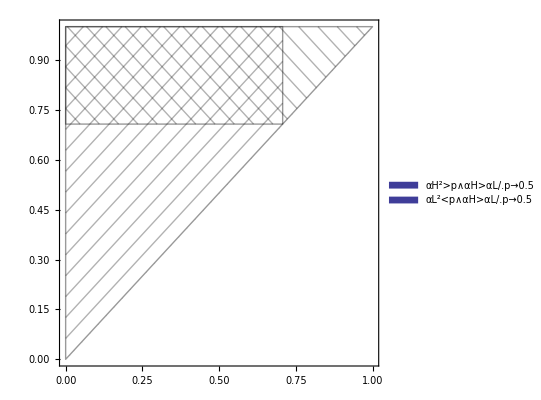

```mathematica
gCombo = Show[{g1,g2}]
```

```mathematica
Export[ "../writeup/images/three_parts.pdf",gCombo]
```

../writeup/images/three_parts.pdf

```mathematica
Solve[-1 +αH + αL == p,αH]
```

{{αH→1+p-αL}}

```mathematica
Manipulate[RegionPlot[{αH^2 > p && αL^2 < p,-1 +αH + αL > p},{αL, 0,1}, {αH,0,1},PlotLegends->"Expressions"],{{p,0.5},0,1}]
```

```mathematica
Manipulate[RegionPlot[{αH^2 >αL,αL^2>αH},{αL, 0,1}, {αH,0,1},PlotLegends->"Expressions"],{{p,0.5},0,1}]
```

### Jevon' s Paradox

As a function of the product market price, what is the fraction of: 
- all buy/no buy/high and lows buy

### Product Market Demand

```mathematica
d[p_]:=If[p > αH^2,0, If[p > αL^2, 1,2]]
```

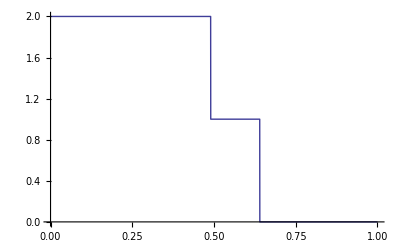

```mathematica
Plot[d[p]/.{αH ->0.8, αL ->0.7},{p,0,1}]
```

```mathematica
2*α*x - x^2 + (1-x)*r - p/.{x->α-r/2}//FullSimplify
```

```mathematica
-p+r+r^2/4-r α+α^2//TeXForm
```

\alpha ^2-p+\frac{r^2}{4}-\alpha  r+r

```mathematica
2*α*x - x^2 - x*r /.{x->α-r/2}//FullSimplify
```

```mathematica
1/4 (r-2 α)^2//TeXForm
```

\frac{1}{4} (r-2 \alpha )^2

```mathematica
-p+r+r^2/4-r α+α^2==1/4 (r-2 α)^2//FullSimplify
```

p==r

## When is demand higher?

```mathematica
Clear[p]
```

```mathematica
conditions = αH>0&&αH < 1 && αL > 0 && αL < 1 && αH> αL && αH^2 > p && αL^2 < p && p > 0
```

αH>0&&αH<1&&αL>0&&αL<1&&αH>αL&&αH^2>p&&αL^2<p&&p>0

```mathematica
Reduce[conditions && (αH + αL) - p>1]//FullSimplify
```

αH<1&&αL^2<p<-1+αH+αL